======================================================

SÍNTESIS CINEMÁTICA Y ANÁLISIS TOPOLÓGICO

======================================================

Eslabones (N): 6 | Juntas (J): 7

Grados de Libertad (F): 1

Espacio Combinatorio Teórico: 6435

Familias Estructurales Encontradas (, , n2n3):

- Familia 1: {4,2}

Procesando matrices de adyacencia y depurando isomorfismos...

-> Familia 1 procesada. Cadenas válidas (KC): 2

======================================================

RESULTADOS: MECANISMOS E INVERSIONES

======================================================

Cadena [1] | Inversiones únicas: 2

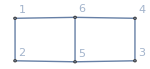
Grafo: -Graphics-

Cadena [2] | Inversiones únicas: 3

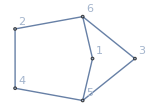
Grafo: -Graphics-

Resumen Topológico Final:

Total de Cadenas Cinemáticas Únicas (KC): 2

Total de Inversiones Cinemáticas (Mecanismos): 5

======================================================

```mathematica
ClearAll["Global`*"];

KinematicSynthesis[Nlinks_Integer,Jjoints_Integer]:=Module[{F,qMax,eq1,eq2,vars,families,combSpace,BocherPolynomial,FilterRigidSubchains,GetDegreeSequences,validChains={},totalMechanisms=0},Print["======================================================"];
Print["      SÍNTESIS CINEMÁTICA Y ANÁLISIS TOPOLÓGICO       "];
Print["======================================================"];
F=3*(Nlinks-1)-2*Jjoints;
combSpace=Binomial[Nlinks*(Nlinks-1)/2,Jjoints];
Print["Eslabones (N): ",Nlinks," | Juntas (J): ",Jjoints];
Print["Grados de Libertad (F): ",F];
Print["Espacio Combinatorio Teórico: ",combSpace];
If[F<0,Print["[!] Error: Grados de libertad negativos."];Return[]];
(*1. Cálculo de Familias Estructurales*)qMax=If[F<=1,Floor[(Nlinks-F+1)/2],Min[Nlinks-F-1,Floor[(Nlinks+F-1)/2]]];
vars=Table[Symbol["n"<>ToString[i]],{i,2,qMax}];
eq1=Total[vars]==Nlinks;
eq2=Sum[i*vars[[i-1]],{i,2,qMax}]==2*Jjoints;
families=Solve[{eq1,eq2,And@@Thread[vars>=0]},vars,Integers];
Print["\nFamilias Estructurales Encontradas (",Row[vars,", "],"):"];
Do[Print[" - Familia ",k,": ",vars/. families[[k]]],{k,1,Length[families]}];
(*2. Pre-filtro Algebraico:Polinomio de Bocher*)BocherPolynomial[adj_?MatrixQ]:=Module[{n,s,a,j,r},n=Length[adj];
s=Table[Tr[MatrixPower[adj,r]],{r,1,n}];
a=ConstantArray[0,n+1];
a[[1]]=1;
For[j=1,j<=n,j++,a[[j+1]]=-1/j*Sum[a[[j-r+1]]*s[[r]],{r,1,j}];];
a];
(*3. FILTRO ESTRICTO DE SUBCADENAS RÍGIDAS (Criterio de Densidad Topológica)*)FilterRigidSubchains[adj_?MatrixQ]:=Catch[Module[{ePrime},(*Conectividad global para eludir el fraccionamiento de la cadena*)If[VertexConnectivity[AdjacencyGraph[adj]]<2,Throw[False]];
(*Condición ineludible de subgrafos:2e'<=3v'-4*)Do[Do[ePrime=Total[adj[[sv,sv]],2]/2;
If[2*ePrime>3*k-4,Throw[False]];,{sv,Subsets[Range[Nlinks],{k}]}];,{k,3,Nlinks-1}];
True]];
GetDegreeSequences[famVals_]:=Flatten[Table[ConstantArray[i+1,famVals[[i]]],{i,1,Length[famVals]}]];
Print["\nProcesando matrices de adyacencia y depurando isomorfismos..."];
(*4. Exploración y Saturación de Secuencias Topológicas*)Do[Module[{degSeq,validGraphsFam={},polyHashes={},adj,pHash,g},degSeq=GetDegreeSequences[vars/. families[[f]]];
(*Muestreo estocástico saturado sobre el espacio paramétrico de secuencias*)Quiet@Do[g=RandomGraph[DegreeGraphDistribution[degSeq]];
If[ConnectedGraphQ[g],adj=Normal[AdjacencyMatrix[g]];
If[FilterRigidSubchains[adj],pHash=BocherPolynomial[adj];
(*Si el polinomio de Bocher es nuevo,es estructuralmente único*)If[!MemberQ[polyHashes,pHash],AppendTo[polyHashes,pHash];
AppendTo[validGraphsFam,g];,(*Ante colisiones polinomiales,ejecutar verificación de isomorfismo profunda*)If[Count[validGraphsFam,x_/;IsomorphicGraphQ[x,g]]==0,AppendTo[polyHashes,pHash];
AppendTo[validGraphsFam,g];];];];];,{5000}];(*La saturación a 5000 ciclos basta para colapsar el espacio en N=8*)validChains=Join[validChains,validGraphsFam];
Print[" -> Familia ",f," procesada. Cadenas válidas (KC): ",Length[validGraphsFam]];],{f,1,Length[families]}];
(*5. Enumeración de Inversiones Cinemáticas (Cálculo de Órbitas de Simetría)*)Print["\n======================================================"];
Print["          RESULTADOS: MECANISMOS E INVERSIONES        "];
Print["======================================================"];
Do[Module[{g,orbits,numInversions},g=validChains[[k]];
orbits=GroupOrbits[GraphAutomorphismGroup[g],VertexList[g]];
numInversions=Length[orbits];
totalMechanisms+=numInversions;
Print["Cadena [",k,"] | Inversiones únicas: ",numInversions];
Print[Row[{"   Grafo: ",Graph[g,VertexLabels->"Name",ImageSize->150]}]];],{k,1,Length[validChains]}];
Print["\nResumen Topológico Final:"];
Print["Total de Cadenas Cinemáticas Únicas (KC): ",Length[validChains]];
Print["Total de Inversiones Cinemáticas (Mecanismos): ",totalMechanisms];
Print["======================================================"];]

(*Ejecución de prueba con el espacio corregido*)
KinematicSynthesis[6,7]
```

======================================================

SÍNTESIS CINEMÁTICA Y ANÁLISIS TOPOLÓGICO

======================================================

Eslabones (N): 8 | Juntas (J): 10

Grados de Libertad (F): 1

Espacio Combinatorio Teórico: 13123110

Familias Estructurales Encontradas (, , n2n3n4):

- Familia 1: {4,4,0}

- Familia 2: {5,2,1}

- Familia 3: {6,0,2}

Procesando matrices de adyacencia y depurando isomorfismos...

-> Familia 1 procesada. Cadenas válidas (KC): 9

-> Familia 2 procesada. Cadenas válidas (KC): 5

-> Familia 3 procesada. Cadenas válidas (KC): 2

======================================================

RESULTADOS: MECANISMOS E INVERSIONES

======================================================

Cadena [1] | Inversiones únicas: 6

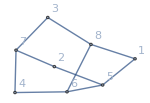
Grafo: -Graphics-

Cadena [2] | Inversiones únicas: 4

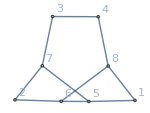
Grafo: -Graphics-

Cadena [3] | Inversiones únicas: 8

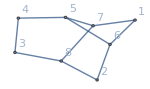
Grafo: -Graphics-

Cadena [4] | Inversiones únicas: 2

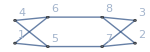
Grafo: -Graphics-

Cadena [5] | Inversiones únicas: 4

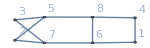
Grafo: -Graphics-

Cadena [6] | Inversiones únicas: 2

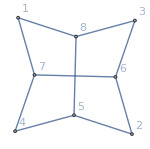
Grafo: -Graphics-

Cadena [7] | Inversiones únicas: 2

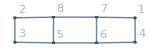
Grafo: -Graphics-

Cadena [8] | Inversiones únicas: 5

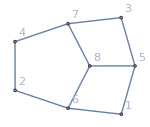
Grafo: -Graphics-

Cadena [9] | Inversiones únicas: 2

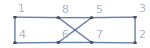
Grafo: -Graphics-

Cadena [10] | Inversiones únicas: 8

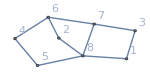
Grafo: -Graphics-

Cadena [11] | Inversiones únicas: 5

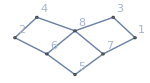
Grafo: -Graphics-

Cadena [12] | Inversiones únicas: 7

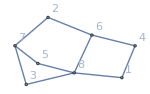
Grafo: -Graphics-

Cadena [13] | Inversiones únicas: 7

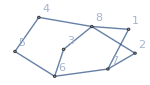
Grafo: -Graphics-

Cadena [14] | Inversiones únicas: 4

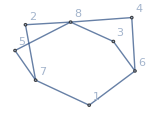
Grafo: -Graphics-

Cadena [15] | Inversiones únicas: 2

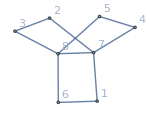
Grafo: -Graphics-

Cadena [16] | Inversiones únicas: 3

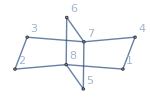
Grafo: -Graphics-

Resumen Topológico Final:

Total de Cadenas Cinemáticas Únicas (KC): 16

Total de Inversiones Cinemáticas (Mecanismos): 71

======================================================

```mathematica
KinematicSynthesis[8,10]
```

======================================================

SÍNTESIS CINEMÁTICA Y ANÁLISIS TOPOLÓGICO

======================================================

Eslabones (N): 10 | Juntas (J): 13

Grados de Libertad (F): 1

Espacio Combinatorio Teórico: 73006209045

Familias Estructurales Encontradas (, , n2n3n4n5):

- Familia 1: {4,6,0,0}

- Familia 2: {5,4,1,0}

- Familia 3: {6,2,2,0}

- Familia 4: {6,3,0,1}

- Familia 5: {7,0,3,0}

- Familia 6: {7,1,1,1}

- Familia 7: {8,0,0,2}

Procesando matrices de adyacencia y depurando isomorfismos...

-> Familia 1 procesada. Cadenas válidas (KC): 50

-> Familia 2 procesada. Cadenas válidas (KC): 95

-> Familia 3 procesada. Cadenas válidas (KC): 57

-> Familia 4 procesada. Cadenas válidas (KC): 15

-> Familia 5 procesada. Cadenas válidas (KC): 3

-> Familia 6 procesada. Cadenas válidas (KC): 8

-> Familia 7 procesada. Cadenas válidas (KC): 2

======================================================

RESULTADOS: MECANISMOS E INVERSIONES

======================================================

Cadena [1] | Inversiones únicas: 10

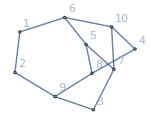
Grafo: -Graphics-

Cadena [2] | Inversiones únicas: 10

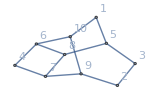
Grafo: -Graphics-

Cadena [3] | Inversiones únicas: 10

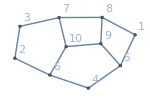
Grafo: -Graphics-

Cadena [4] | Inversiones únicas: 10

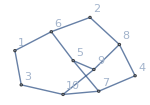
Grafo: -Graphics-

Cadena [5] | Inversiones únicas: 10

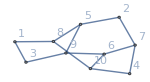
Grafo: -Graphics-

Cadena [6] | Inversiones únicas: 10

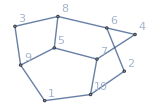
Grafo: -Graphics-

Cadena [7] | Inversiones únicas: 6

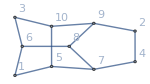
Grafo: -Graphics-

Cadena [8] | Inversiones únicas: 10

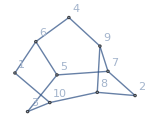
Grafo: -Graphics-

Cadena [9] | Inversiones únicas: 10

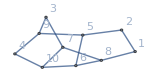
Grafo: -Graphics-

Cadena [10] | Inversiones únicas: 10

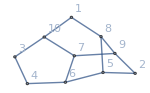
Grafo: -Graphics-

Cadena [11] | Inversiones únicas: 7

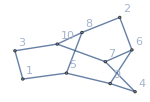
Grafo: -Graphics-

Cadena [12] | Inversiones únicas: 6

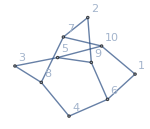
Grafo: -Graphics-

Cadena [13] | Inversiones únicas: 10

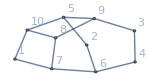
Grafo: -Graphics-

Cadena [14] | Inversiones únicas: 5

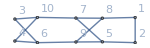
Grafo: -Graphics-

Cadena [15] | Inversiones únicas: 5

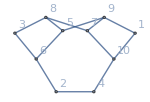
Grafo: -Graphics-

Cadena [16] | Inversiones únicas: 6

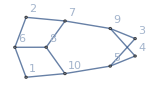
Grafo: -Graphics-

Cadena [17] | Inversiones únicas: 6

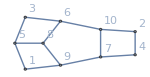
Grafo: -Graphics-

Cadena [18] | Inversiones únicas: 6

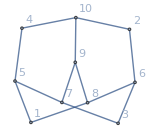
Grafo: -Graphics-

Cadena [19] | Inversiones únicas: 5

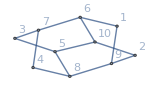
Grafo: -Graphics-

Cadena [20] | Inversiones únicas: 10

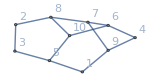
Grafo: -Graphics-

Cadena [21] | Inversiones únicas: 3

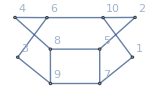
Grafo: -Graphics-

Cadena [22] | Inversiones únicas: 6

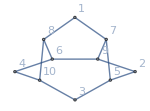
Grafo: -Graphics-

Cadena [23] | Inversiones únicas: 5

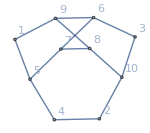
Grafo: -Graphics-

Cadena [24] | Inversiones únicas: 5

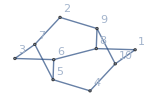
Grafo: -Graphics-

Cadena [25] | Inversiones únicas: 7

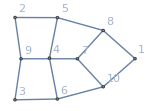
Grafo: -Graphics-

Cadena [26] | Inversiones únicas: 5

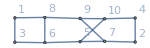
Grafo: -Graphics-

Cadena [27] | Inversiones únicas: 10

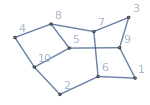
Grafo: -Graphics-

Cadena [28] | Inversiones únicas: 10

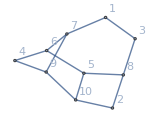
Grafo: -Graphics-

Cadena [29] | Inversiones únicas: 10

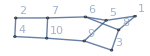
Grafo: -Graphics-

Cadena [30] | Inversiones únicas: 9

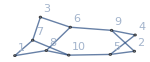
Grafo: -Graphics-

Cadena [31] | Inversiones únicas: 5

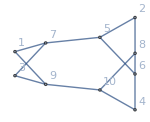
Grafo: -Graphics-

Cadena [32] | Inversiones únicas: 10

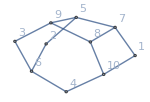
Grafo: -Graphics-

Cadena [33] | Inversiones únicas: 10

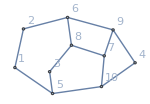
Grafo: -Graphics-

Cadena [34] | Inversiones únicas: 3

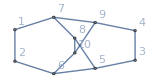
Grafo: -Graphics-

Cadena [35] | Inversiones únicas: 5

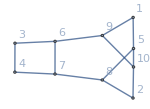
Grafo: -Graphics-

Cadena [36] | Inversiones únicas: 8

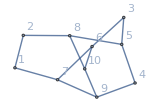
Grafo: -Graphics-

Cadena [37] | Inversiones únicas: 5

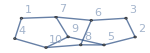
Grafo: -Graphics-

Cadena [38] | Inversiones únicas: 10

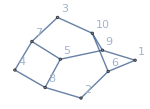
Grafo: -Graphics-

Cadena [39] | Inversiones únicas: 7

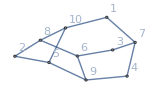
Grafo: -Graphics-

Cadena [40] | Inversiones únicas: 5

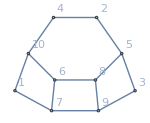
Grafo: -Graphics-

Cadena [41] | Inversiones únicas: 4

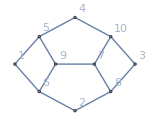
Grafo: -Graphics-

Cadena [42] | Inversiones únicas: 4

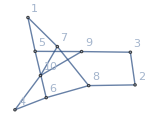
Grafo: -Graphics-

Cadena [43] | Inversiones únicas: 3

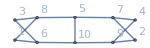
Grafo: -Graphics-

Cadena [44] | Inversiones únicas: 5

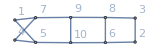
Grafo: -Graphics-

Cadena [45] | Inversiones únicas: 4

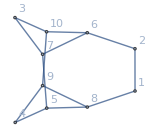
Grafo: -Graphics-

Cadena [46] | Inversiones únicas: 8

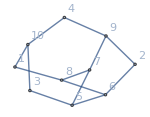
Grafo: -Graphics-

Cadena [47] | Inversiones únicas: 3

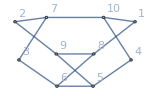
Grafo: -Graphics-

Cadena [48] | Inversiones únicas: 3

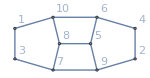
Grafo: -Graphics-

Cadena [49] | Inversiones únicas: 3

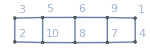
Grafo: -Graphics-

Cadena [50] | Inversiones únicas: 3

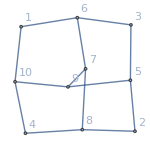
Grafo: -Graphics-

Cadena [51] | Inversiones únicas: 9

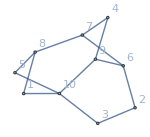
Grafo: -Graphics-

Cadena [52] | Inversiones únicas: 9

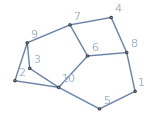
Grafo: -Graphics-

Cadena [53] | Inversiones únicas: 10

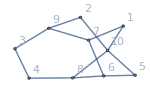
Grafo: -Graphics-

Cadena [54] | Inversiones únicas: 10

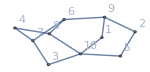
Grafo: -Graphics-

Cadena [55] | Inversiones únicas: 7

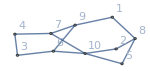
Grafo: -Graphics-

Cadena [56] | Inversiones únicas: 10

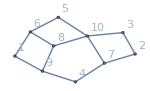
Grafo: -Graphics-

Cadena [57] | Inversiones únicas: 6

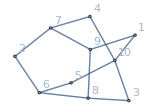
Grafo: -Graphics-

Cadena [58] | Inversiones únicas: 6

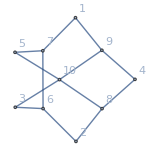
Grafo: -Graphics-

Cadena [59] | Inversiones únicas: 9

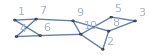
Grafo: -Graphics-

Cadena [60] | Inversiones únicas: 10

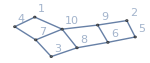
Grafo: -Graphics-

Cadena [61] | Inversiones únicas: 10

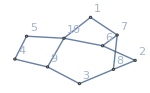
Grafo: -Graphics-

Cadena [62] | Inversiones únicas: 9

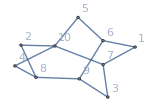
Grafo: -Graphics-

Cadena [63] | Inversiones únicas: 10

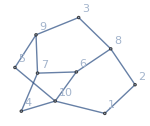
Grafo: -Graphics-

Cadena [64] | Inversiones únicas: 8

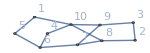
Grafo: -Graphics-

Cadena [65] | Inversiones únicas: 10

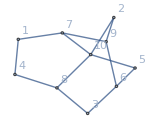
Grafo: -Graphics-

Cadena [66] | Inversiones únicas: 10

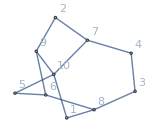
Grafo: -Graphics-

Cadena [67] | Inversiones únicas: 10

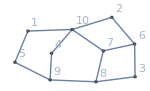
Grafo: -Graphics-

Cadena [68] | Inversiones únicas: 10

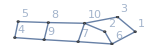
Grafo: -Graphics-

Cadena [69] | Inversiones únicas: 10

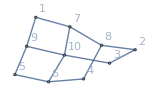
Grafo: -Graphics-

Cadena [70] | Inversiones únicas: 10

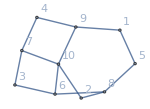
Grafo: -Graphics-

Cadena [71] | Inversiones únicas: 10

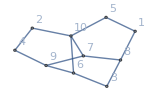
Grafo: -Graphics-

Cadena [72] | Inversiones únicas: 7

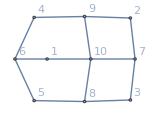
Grafo: -Graphics-

Cadena [73] | Inversiones únicas: 10

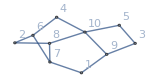
Grafo: -Graphics-

Cadena [74] | Inversiones únicas: 10

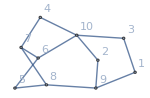
Grafo: -Graphics-

Cadena [75] | Inversiones únicas: 10

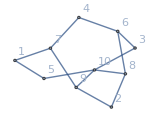
Grafo: -Graphics-

Cadena [76] | Inversiones únicas: 10

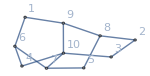
Grafo: -Graphics-

Cadena [77] | Inversiones únicas: 10

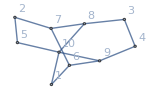
Grafo: -Graphics-

Cadena [78] | Inversiones únicas: 10

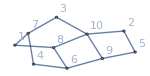
Grafo: -Graphics-

Cadena [79] | Inversiones únicas: 10

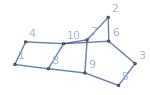
Grafo: -Graphics-

Cadena [80] | Inversiones únicas: 7

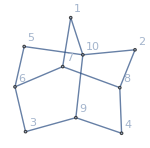
Grafo: -Graphics-

Cadena [81] | Inversiones únicas: 10

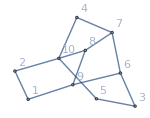
Grafo: -Graphics-

Cadena [82] | Inversiones únicas: 10

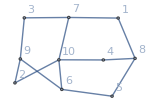
Grafo: -Graphics-

Cadena [83] | Inversiones únicas: 10

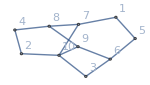
Grafo: -Graphics-

Cadena [84] | Inversiones únicas: 8

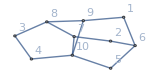
Grafo: -Graphics-

Cadena [85] | Inversiones únicas: 10

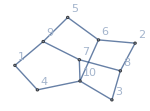
Grafo: -Graphics-

Cadena [86] | Inversiones únicas: 10

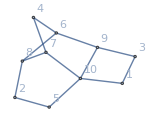
Grafo: -Graphics-

Cadena [87] | Inversiones únicas: 9

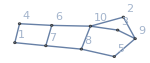
Grafo: -Graphics-

Cadena [88] | Inversiones únicas: 10

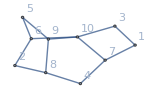
Grafo: -Graphics-

Cadena [89] | Inversiones únicas: 10

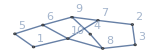
Grafo: -Graphics-

Cadena [90] | Inversiones únicas: 10

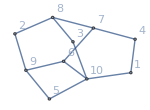
Grafo: -Graphics-

Cadena [91] | Inversiones únicas: 8

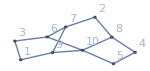
Grafo: -Graphics-

Cadena [92] | Inversiones únicas: 10

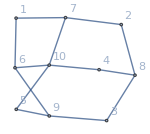
Grafo: -Graphics-

Cadena [93] | Inversiones únicas: 9

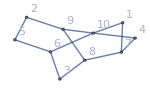
Grafo: -Graphics-

Cadena [94] | Inversiones únicas: 10

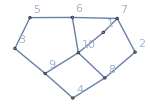
Grafo: -Graphics-

Cadena [95] | Inversiones únicas: 9

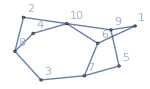
Grafo: -Graphics-

Cadena [96] | Inversiones únicas: 10

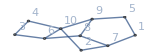
Grafo: -Graphics-

Cadena [97] | Inversiones únicas: 10

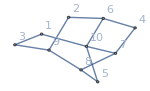
Grafo: -Graphics-

Cadena [98] | Inversiones únicas: 10

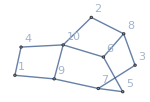
Grafo: -Graphics-

Cadena [99] | Inversiones únicas: 10

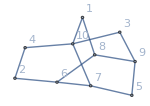
Grafo: -Graphics-

Cadena [100] | Inversiones únicas: 10

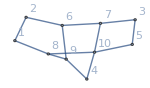
Grafo: -Graphics-

Cadena [101] | Inversiones únicas: 10

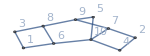
Grafo: -Graphics-

Cadena [102] | Inversiones únicas: 10

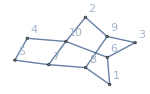
Grafo: -Graphics-

Cadena [103] | Inversiones únicas: 10

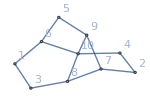
Grafo: -Graphics-

Cadena [104] | Inversiones únicas: 10

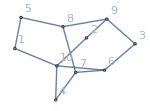
Grafo: -Graphics-

Cadena [105] | Inversiones únicas: 10

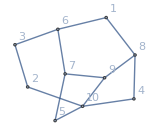
Grafo: -Graphics-

Cadena [106] | Inversiones únicas: 10

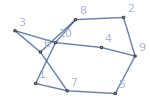
Grafo: -Graphics-

Cadena [107] | Inversiones únicas: 10

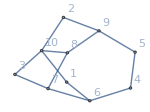
Grafo: -Graphics-

Cadena [108] | Inversiones únicas: 9

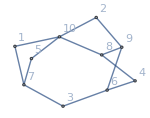
Grafo: -Graphics-

Cadena [109] | Inversiones únicas: 9

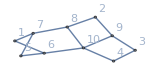
Grafo: -Graphics-

Cadena [110] | Inversiones únicas: 10

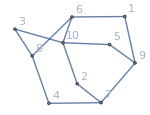
Grafo: -Graphics-

Cadena [111] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [112] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [113] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [114] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [115] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [116] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [117] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [118] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [119] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [120] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [121] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [122] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [123] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [124] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [125] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [126] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [127] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [128] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [129] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [130] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [131] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [132] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [133] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [134] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [135] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [136] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [137] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [138] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [139] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [140] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [141] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [142] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [143] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [144] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [145] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [146] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [147] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [148] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [149] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [150] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [151] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [152] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [153] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [154] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [155] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [156] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [157] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [158] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [159] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [160] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [161] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [162] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [163] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [164] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [165] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [166] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [167] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [168] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [169] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [170] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [171] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [172] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [173] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [174] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [175] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [176] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [177] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [178] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [179] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [180] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [181] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [182] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [183] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [184] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [185] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [186] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [187] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [188] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [189] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [190] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [191] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [192] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [193] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [194] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [195] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [196] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [197] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [198] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [199] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [200] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [201] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [202] | Inversiones únicas: 4

Grafo: -Graphics-

Cadena [203] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [204] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [205] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [206] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [207] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [208] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [209] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [210] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [211] | Inversiones únicas: 10

Grafo: -Graphics-

Cadena [212] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [213] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [214] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [215] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [216] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [217] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [218] | Inversiones únicas: 6

Grafo: -Graphics-

Cadena [219] | Inversiones únicas: 5

Grafo: -Graphics-

Cadena [220] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [221] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [222] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [223] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [224] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [225] | Inversiones únicas: 9

Grafo: -Graphics-

Cadena [226] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [227] | Inversiones únicas: 7

Grafo: -Graphics-

Cadena [228] | Inversiones únicas: 8

Grafo: -Graphics-

Cadena [229] | Inversiones únicas: 3

Grafo: -Graphics-

Cadena [230] | Inversiones únicas: 2

Grafo: -Graphics-

Resumen Topológico Final:

Total de Cadenas Cinemáticas Únicas (KC): 230

Total de Inversiones Cinemáticas (Mecanismos): 1834

======================================================

```mathematica
KinematicSynthesis[10,13]
```